```mathematica
Clear[coord,metric,inversemetric, det, affine,riemann,ricci,upperIndexRiemann,scalarRicci, Kretschman, listaffine, listricci, listriemann,x,y,ϕ,t,f, g,A3, det, α,i,j,k,l,s,n]
```

```mathematica
coord:={t,x,y,ϕ}
```

```mathematica
n := 4
```

```mathematica
metric:={{-f[x,y]^2*(x-1)/(x+1),0,0,0},{0,(g[x,y]/f[x,y])^2 * ((x+1)/(x-1)),0,0},{0,0,(g[x,y]/f[x,y])^2 * ((x+1)^2/(1-y^2)),0},{0,0,0,k^2 * (x +1)^2 *(1-y^2)/(f[x,y]^2)}}
```

```mathematica
inversemetric:=Simplify[Inverse[metric]]
```

```mathematica
f[x_,y_] := ((x^2 - y^2 + α^2 *(x^2 - 1))^2 + 4 * α^2 *x^2 *(1 - y^2) )/((x^2 - y^2 + α^2 *(x- 1)^2)^2 - 4 * α^2 *y^2 *(x^2 - 1))
```

```mathematica
g[x_,y_] := ((x^2 - y^2 + α^2 *(x^2 - 1))^2 + 4 * α^2 *x^2 *(1 - y^2) )^2/((α^2 +1)^4 *(x^2 - y^2)^4 )
```

```mathematica
A3[x,y] = (4*α^3)/(1+α^2)*((1-y^2)*(2*(1+α^2)x^3 + (1-3α^2)x^2  + y^2 + α^2))/((x^2 - y^2 + α^2 *(x^2 - 1))^2 - 4 * α^2 *y^2 *(x^2 - 1))
```

(4 (1-y^2) α^3 (y^2+α^2+x^2 (1-3 α^2)+2 x^3 (1+α^2)))/((1+α^2) (-4 (-1+x^2) y^2 α^2+(x^2-y^2+(-1+x^2) α^2)^2))

```mathematica
affine:=affine=Simplify[Table[(1/2)*Sum[(inversemetric⟦i,s⟧)*(D[metric⟦s,j⟧,coord⟦k⟧]+D[metric⟦s,k⟧,coord[[j]]]-D[metric⟦j,k⟧,coord[[s]]]),{s,1,n}],{i,1,n},{j,1,n},{k,1,n}]]
```

```mathematica
listaffine:=Table[If[UnsameQ[affine⟦i,j,k⟧,0],{Subsuperscript[Γ,ToString["  "]<>ToString[(j-1)]<>ToString[" "]<>ToString[(k-1)],ToString[(i-1)]],"=" ,affine⟦i,j,k⟧}],{i,1,n},{j,1,n},{k,1,n}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listaffine],Null],3],TableSpacing->{3,1,3}]
```

Γ_(0 1)^0 | = | (y^8+8 y^6 α^2+10 y^4 α^4-3 α^8-x^8 (1+α^2)^3 (-1+3 α^2)+4 x α^2 (y^2+α^2)^2 (y^2+3 α^2)+4 x^7 (-1+3 α^2) (α+α^3)^2+4 x^5 α^2 (1+α^2) (-α^2 (7+3 α^2)+y^2 (3+7 α^2))-4 x^2 (3 α^8+y^4 α^2 (2+3 α^2)+y^6 (1+4 α^2)+y^2 α^4 (9+10 α^2))-4 x^6 (1+α^2) (α^2 (-2-3 α^2+3 α^4)+y^2 (1+3 α^2+6 α^4))+2 x^4 (1+α^2) (4 y^2 α^2 (-1+4 α^2)+y^4 (3+13 α^2)+5 (α^4+3 α^6))-4 x^3 (y^4 α^2 (3+11 α^2)+y^2 (-2 α^4+6 α^6)+3 (α^6+α^8)))/((-1+x) (1+x) (4 x α^2 (y^2-α^2)+x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2) (1+3 α^2)-4 x^3 (α^2+α^4)) (x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2+3 y^2 α^2+α^4)))
Γ_(0 2)^0 | = | (8 x y α^2 (y^4-2 y^2 α^2-3 α^4+4 x α^2 (y^2+α^2)-4 x^3 (α^2+3 α^4)+x^4 (1+6 α^2+5 α^4)-2 x^2 (α^2-3 α^4+y^2 (1+α^2))))/((4 x α^2 (y^2-α^2)+x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2) (1+3 α^2)-4 x^3 (α^2+α^4)) (x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2+3 y^2 α^2+α^4)))
Γ_(1 0)^0 | = | (y^8+8 y^6 α^2+10 y^4 α^4-3 α^8-x^8 (1+α^2)^3 (-1+3 α^2)+4 x α^2 (y^2+α^2)^2 (y^2+3 α^2)+4 x^7 (-1+3 α^2) (α+α^3)^2+4 x^5 α^2 (1+α^2) (-α^2 (7+3 α^2)+y^2 (3+7 α^2))-4 x^2 (3 α^8+y^4 α^2 (2+3 α^2)+y^6 (1+4 α^2)+y^2 α^4 (9+10 α^2))-4 x^6 (1+α^2) (α^2 (-2-3 α^2+3 α^4)+y^2 (1+3 α^2+6 α^4))+2 x^4 (1+α^2) (4 y^2 α^2 (-1+4 α^2)+y^4 (3+13 α^2)+5 (α^4+3 α^6))-4 x^3 (y^4 α^2 (3+11 α^2)+y^2 (-2 α^4+6 α^6)+3 (α^6+α^8)))/((-1+x) (1+x) (4 x α^2 (y^2-α^2)+x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2) (1+3 α^2)-4 x^3 (α^2+α^4)) (x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2+3 y^2 α^2+α^4)))
Γ_(2 0)^0 | = | (8 x y α^2 (y^4-2 y^2 α^2-3 α^4+4 x α^2 (y^2+α^2)-4 x^3 (α^2+3 α^4)+x^4 (1+6 α^2+5 α^4)-2 x^2 (α^2-3 α^4+y^2 (1+α^2))))/((4 x α^2 (y^2-α^2)+x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2) (1+3 α^2)-4 x^3 (α^2+α^4)) (x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2+3 y^2 α^2+α^4)))
Γ_(0 0)^1 | = | -((-1+x) (x^2-y^2)^8 (1+α^2)^8 (x^8 (1+α^2)^3 (-1+3 α^2)-4 x α^2 (y^2+α^2)^2 (y^2+3 α^2)-4 x^7 (-1+3 α^2) (α+α^3)^2-(y^2+α^2)^2 (y^4+6 y^2 α^2-3 α^4)+4 x^5 α^2 (1+α^2) (α^2 (7+3 α^2)-y^2 (3+7 α^2))+4 x^2 (3 α^8+y^4 α^2 (2+3 α^2)+y^6 (1+4 α^2)+y^2 α^4 (9+10 α^2))+4 x^6 (1+α^2) (α^2 (-2-3 α^2+3 α^4)+y^2 (1+3 α^2+6 α^4))-2 x^4 (1+α^2) (4 y^2 α^2 (-1+4 α^2)+y^4 (3+13 α^2)+5 (α^4+3 α^6))+4 x^3 (y^4 α^2 (3+11 α^2)+y^2 (-2 α^4+6 α^6)+3 (α^6+α^8))))/((1+x)^3 (4 x α^2 (y^2-α^2)+x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2) (1+3 α^2)-4 x^3 (α^2+α^4))^5 (x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2+3 y^2 α^2+α^4)))
Γ_(1 1)^1 | = | 1/(2-2 x)+1/(2+2 x)-(8 x)/(x^2-y^2)+(-8 x y^2 α^2+4 (x+(-1+x) α^2) (x^2-y^2+(-1+x)^2 α^2))/(-4 (-1+x^2) y^2 α^2+(x^2-y^2+(-1+x)^2 α^2)^2)+(4 x (α^2-α^4+x^2 (1+α^2)^2-y^2 (1+3 α^2)))/(-4 x^2 (-1+y^2) α^2+(x^2-y^2+(-1+x^2) α^2)^2)
Γ_(1 2)^1 | = | (8 y α^2 (x^8 (-1+α^2) (1+α^2)^2+(y^2+α^2)^3+x (y^6+2 y^4 α^2-3 y^2 α^4-4 α^6)-x^7 (1+2 α^2+5 α^4+4 α^6)+x^2 (-3 y^6+y^4 (1-10 α^2)-3 y^2 α^2 (-2+α^2)+α^4 (5+4 α^2))+x^3 (α^4 (-13+4 α^2)-y^4 (3+14 α^2)+y^2 (8 α^2+6 α^4))+x^6 (3+6 α^2+7 α^4+4 α^6-y^2 (1+2 α^2+9 α^4))+x^4 (7 α^2+11 α^4-10 α^6+y^4 (5+19 α^2)-y^2 (5+28 α^2+15 α^4))+x^5 (2 α^2 (-5-3 α^2+2 α^4)+y^2 (3+16 α^2+21 α^4))))/((x^2-y^2) (4 x α^2 (y^2-α^2)+x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2) (1+3 α^2)-4 x^3 (α^2+α^4)) (x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2+3 y^2 α^2+α^4)))
Γ_(2 1)^1 | = | (8 y α^2 (x^8 (-1+α^2) (1+α^2)^2+(y^2+α^2)^3+x (y^6+2 y^4 α^2-3 y^2 α^4-4 α^6)-x^7 (1+2 α^2+5 α^4+4 α^6)+x^2 (-3 y^6+y^4 (1-10 α^2)-3 y^2 α^2 (-2+α^2)+α^4 (5+4 α^2))+x^3 (α^4 (-13+4 α^2)-y^4 (3+14 α^2)+y^2 (8 α^2+6 α^4))+x^6 (3+6 α^2+7 α^4+4 α^6-y^2 (1+2 α^2+9 α^4))+x^4 (7 α^2+11 α^4-10 α^6+y^4 (5+19 α^2)-y^2 (5+28 α^2+15 α^4))+x^5 (2 α^2 (-5-3 α^2+2 α^4)+y^2 (3+16 α^2+21 α^4))))/((x^2-y^2) (4 x α^2 (y^2-α^2)+x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2) (1+3 α^2)-4 x^3 (α^2+α^4)) (x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2+3 y^2 α^2+α^4)))
Γ_(2 2)^1 | = | ((-1+x) (x^10 (1+α^2)^4-8 x α^2 (y^2+α^2)^2 (3 y^2-2 y^4+α^2)-y^2 (y^2+α^2)^2 (y^4+6 y^2 α^2-3 α^4)-x^8 y^2 (1+α^2)^2 (5+6 α^2+9 α^4)+x^2 (21 α^8-24 y^2 α^6 (-1+α^2)-2 y^4 α^4 (53+6 α^2)+8 y^6 α^2 (-1+18 α^2)+y^8 (5+36 α^2))+8 x^7 α^2 (1+α^2) (-1+α^2-2 α^4+y^2 (2+α^2+3 α^4))-8 x^5 α^2 (1+α^2) (-3 α^2 (-1+α^2)+2 y^4 (1+6 α^2)+y^2 (1-9 α^2+6 α^4))-8 x^3 α^2 (3 α^4+y^6 (2+5 α^2)-3 y^2 α^2 (-2+2 α^2+α^4)-y^4 (5+20 α^2+6 α^4))+2 x^6 (9 α^4-6 α^6+9 α^8-12 y^2 (α+α^3)^2+y^4 (5+28 α^2+41 α^4+42 α^6))-10 x^4 (4 α^6 (-1+α^2)+4 y^4 α^2 (-1-4 α^2+α^4)+y^6 (1+8 α^2+19 α^4)+y^2 (3 α^4+4 α^6-3 α^8))))/((x^2-y^2) (-1+y^2) (4 x α^2 (y^2-α^2)+x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2) (1+3 α^2)-4 x^3 (α^2+α^4)) (x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2+3 y^2 α^2+α^4)))
Γ_(3 3)^1 | = | (16 (-1+x) (1-y^2) (x^2-y^2)^8 (1+α^2)^8 (4 x (1+x) (α^2-α^4+x^2 (1+α^2)^2-y^2 (1+3 α^2)) (-4 (-1+x^2) y^2 α^2+(x^2-y^2+(-1+x)^2 α^2)^2)-(1+x) (-8 x y^2 α^2+4 (x+(-1+x) α^2) (x^2-y^2+(-1+x)^2 α^2)) (-4 x^2 (-1+y^2) α^2+(x^2-y^2+(-1+x^2) α^2)^2)-(-4 (-1+x^2) y^2 α^2+(x^2-y^2+(-1+x)^2 α^2)^2) (-4 x^2 (-1+y^2) α^2+(x^2-y^2+(-1+x^2) α^2)^2)))/((-4 (-1+x^2) y^2 α^2+(x^2-y^2+(-1+x)^2 α^2)^2) (-4 x^2 (-1+y^2) α^2+(x^2-y^2+(-1+x^2) α^2)^2)^5)
Γ_(0 0)^2 | = | -(8 (-1+x) x y (x^2-y^2)^8 (-1+y^2) α^2 (1+α^2)^8 (y^4-2 y^2 α^2-3 α^4+4 x α^2 (y^2+α^2)-4 x^3 (α^2+3 α^4)+x^4 (1+6 α^2+5 α^4)-2 x^2 (α^2-3 α^4+y^2 (1+α^2))))/((1+x)^3 (4 x α^2 (y^2-α^2)+x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2) (1+3 α^2)-4 x^3 (α^2+α^4))^5 (x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2+3 y^2 α^2+α^4)))
Γ_(1 1)^2 | = | (8 y (-1+y^2) α^2 (x^8 (-1+α^2) (1+α^2)^2+(y^2+α^2)^3+x (y^6+2 y^4 α^2-3 y^2 α^4-4 α^6)-x^7 (1+2 α^2+5 α^4+4 α^6)+x^2 (-3 y^6+y^4 (1-10 α^2)-3 y^2 α^2 (-2+α^2)+α^4 (5+4 α^2))+x^3 (α^4 (-13+4 α^2)-y^4 (3+14 α^2)+y^2 (8 α^2+6 α^4))+x^6 (3+6 α^2+7 α^4+4 α^6-y^2 (1+2 α^2+9 α^4))+x^4 (7 α^2+11 α^4-10 α^6+y^4 (5+19 α^2)-y^2 (5+28 α^2+15 α^4))+x^5 (2 α^2 (-5-3 α^2+2 α^4)+y^2 (3+16 α^2+21 α^4))))/((-1+x) (1+x) (x^2-y^2) (4 x α^2 (y^2-α^2)+x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2) (1+3 α^2)-4 x^3 (α^2+α^4)) (x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2+3 y^2 α^2+α^4)))
Γ_(1 2)^2 | = | (x^10 (1+α^2)^4-8 x α^2 (y^2+α^2)^2 (3 y^2-2 y^4+α^2)-y^2 (y^2+α^2)^2 (y^4+6 y^2 α^2-3 α^4)-x^8 y^2 (1+α^2)^2 (5+6 α^2+9 α^4)+x^2 (21 α^8-24 y^2 α^6 (-1+α^2)-2 y^4 α^4 (53+6 α^2)+8 y^6 α^2 (-1+18 α^2)+y^8 (5+36 α^2))+8 x^7 α^2 (1+α^2) (-1+α^2-2 α^4+y^2 (2+α^2+3 α^4))-8 x^5 α^2 (1+α^2) (-3 α^2 (-1+α^2)+2 y^4 (1+6 α^2)+y^2 (1-9 α^2+6 α^4))-8 x^3 α^2 (3 α^4+y^6 (2+5 α^2)-3 y^2 α^2 (-2+2 α^2+α^4)-y^4 (5+20 α^2+6 α^4))+2 x^6 (9 α^4-6 α^6+9 α^8-12 y^2 (α+α^3)^2+y^4 (5+28 α^2+41 α^4+42 α^6))-10 x^4 (4 α^6 (-1+α^2)+4 y^4 α^2 (-1-4 α^2+α^4)+y^6 (1+8 α^2+19 α^4)+y^2 (3 α^4+4 α^6-3 α^8)))/((1+x) (x^2-y^2) (4 x α^2 (y^2-α^2)+x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2) (1+3 α^2)-4 x^3 (α^2+α^4)) (x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2+3 y^2 α^2+α^4)))
Γ_(2 1)^2 | = | (x^10 (1+α^2)^4-8 x α^2 (y^2+α^2)^2 (3 y^2-2 y^4+α^2)-y^2 (y^2+α^2)^2 (y^4+6 y^2 α^2-3 α^4)-x^8 y^2 (1+α^2)^2 (5+6 α^2+9 α^4)+x^2 (21 α^8-24 y^2 α^6 (-1+α^2)-2 y^4 α^4 (53+6 α^2)+8 y^6 α^2 (-1+18 α^2)+y^8 (5+36 α^2))+8 x^7 α^2 (1+α^2) (-1+α^2-2 α^4+y^2 (2+α^2+3 α^4))-8 x^5 α^2 (1+α^2) (-3 α^2 (-1+α^2)+2 y^4 (1+6 α^2)+y^2 (1-9 α^2+6 α^4))-8 x^3 α^2 (3 α^4+y^6 (2+5 α^2)-3 y^2 α^2 (-2+2 α^2+α^4)-y^4 (5+20 α^2+6 α^4))+2 x^6 (9 α^4-6 α^6+9 α^8-12 y^2 (α+α^3)^2+y^4 (5+28 α^2+41 α^4+42 α^6))-10 x^4 (4 α^6 (-1+α^2)+4 y^4 α^2 (-1-4 α^2+α^4)+y^6 (1+8 α^2+19 α^4)+y^2 (3 α^4+4 α^6-3 α^8)))/((1+x) (x^2-y^2) (4 x α^2 (y^2-α^2)+x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2) (1+3 α^2)-4 x^3 (α^2+α^4)) (x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2+3 y^2 α^2+α^4)))
Γ_(2 2)^2 | = | (y (1-y^2+(8-8 y^2)/(x^2-y^2)-(8 y^2 (-1+y^2))/(-x^2+y^2)+(4 (1-y^2) (y^2+α^2+2 x α^2-x^2 (1+3 α^2)))/(-4 (-1+x^2) y^2 α^2+(x^2-y^2+(-1+x)^2 α^2)^2)-(4 y^2 (1-y^2) (y^2+α^2+2 x α^2-x^2 (1+3 α^2)))/(-4 (-1+x^2) y^2 α^2+(x^2-y^2+(-1+x)^2 α^2)^2)+(4 (1-y^2) (y^2+α^2-x^2 (1+3 α^2)))/(-4 x^2 (-1+y^2) α^2+(x^2-y^2+(-1+x^2) α^2)^2)-(4 y^2 (1-y^2) (y^2+α^2-x^2 (1+3 α^2)))/(-4 x^2 (-1+y^2) α^2+(x^2-y^2+(-1+x^2) α^2)^2)))/((-1+y^2)^2)
Γ_(3 3)^2 | = | (16 y (1-y^2) (x^2-y^2)^8 (1+α^2)^8 (4 (1-y^2) (y^2+α^2-x^2 (1+3 α^2)) (-4 (-1+x^2) y^2 α^2+(x^2-y^2+(-1+x)^2 α^2)^2)-4 (1-y^2) (y^2+α^2+2 x α^2-x^2 (1+3 α^2)) (-4 x^2 (-1+y^2) α^2+(x^2-y^2+(-1+x^2) α^2)^2)+(-4 (-1+x^2) y^2 α^2+(x^2-y^2+(-1+x)^2 α^2)^2) (-4 x^2 (-1+y^2) α^2+(x^2-y^2+(-1+x^2) α^2)^2)))/((-4 (-1+x^2) y^2 α^2+(x^2-y^2+(-1+x)^2 α^2)^2) (-4 x^2 (-1+y^2) α^2+(x^2-y^2+(-1+x^2) α^2)^2)^5)
Γ_(1 3)^3 | = | (y^8+8 y^6 α^2+10 y^4 α^4-3 α^8+x^8 (1+α^2)^4-16 x^3 α^2 (1+α^2) (y^2+α^2)^2+8 x α^2 (y^2+α^2)^3+8 x^5 α^2 (1+α^2) (y^2-3 α^2+5 y^2 α^2+α^4)-4 x^6 (1+α^2)^2 (2 α^2 (-1+α^2)+y^2 (1+3 α^2))-4 x^2 (-2 y^4 α^2 (-1+α^2)+3 y^2 α^4 (3+α^2)+y^6 (1+3 α^2))+2 x^4 (-4 y^2 (α+α^3)^2+α^4 (5+18 α^2+5 α^4)+y^4 (3+14 α^2+19 α^4)))/((1+x) (4 x α^2 (y^2-α^2)+x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2) (1+3 α^2)-4 x^3 (α^2+α^4)) (x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2+3 y^2 α^2+α^4)))
Γ_(2 3)^3 | = | (y (4 x^2 α^2+4 (x^2-y^2+(-1+x^2) α^2)+((y^2+α^2-x^2 (1+α^2))^2)/(-1+y^2)+(4 (y^2+α^2+2 x α^2-x^2 (1+3 α^2)) (-4 x^2 (-1+y^2) α^2+(x^2-y^2+(-1+x^2) α^2)^2))/(-4 (-1+x^2) y^2 α^2+(x^2-y^2+(-1+x)^2 α^2)^2)))/(-4 x^2 (-1+y^2) α^2+(x^2-y^2+(-1+x^2) α^2)^2)
Γ_(3 1)^3 | = | (y^8+8 y^6 α^2+10 y^4 α^4-3 α^8+x^8 (1+α^2)^4-16 x^3 α^2 (1+α^2) (y^2+α^2)^2+8 x α^2 (y^2+α^2)^3+8 x^5 α^2 (1+α^2) (y^2-3 α^2+5 y^2 α^2+α^4)-4 x^6 (1+α^2)^2 (2 α^2 (-1+α^2)+y^2 (1+3 α^2))-4 x^2 (-2 y^4 α^2 (-1+α^2)+3 y^2 α^4 (3+α^2)+y^6 (1+3 α^2))+2 x^4 (-4 y^2 (α+α^3)^2+α^4 (5+18 α^2+5 α^4)+y^4 (3+14 α^2+19 α^4)))/((1+x) (4 x α^2 (y^2-α^2)+x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2) (1+3 α^2)-4 x^3 (α^2+α^4)) (x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2+3 y^2 α^2+α^4)))
Γ_(3 2)^3 | = | (y (4 x^2 α^2+4 (x^2-y^2+(-1+x^2) α^2)+((y^2+α^2-x^2 (1+α^2))^2)/(-1+y^2)+(4 (y^2+α^2+2 x α^2-x^2 (1+3 α^2)) (-4 x^2 (-1+y^2) α^2+(x^2-y^2+(-1+x^2) α^2)^2))/(-4 (-1+x^2) y^2 α^2+(x^2-y^2+(-1+x)^2 α^2)^2)))/(-4 x^2 (-1+y^2) α^2+(x^2-y^2+(-1+x^2) α^2)^2)

```mathematica
riemann:=riemann=Simplify[Table[D[affine⟦i,j,l⟧,coord[[k]]]-D[affine⟦i,j,k⟧,coord[[l]]]+Sum[affine⟦s,j,l⟧* affine⟦i,k,s⟧ -affine⟦s,j,k⟧*affine⟦i,l,s⟧,{s,1,n}],{i,1,n},{j,1,n},{k,1,n},{l,1,n}]]
```

```mathematica
listriemann:=Table[If[UnsameQ[riemann⟦i,j,k,l⟧,0],{Subsuperscript[R,ToString["  "]<>ToString[j-1]<>ToString[k-1]<>ToString[l-1],ToString[i-1]],"=",riemann⟦i,j,k,l⟧}],{i,1,n},{j,1,n},{j,1,n},{k,1,n},{l,1,n}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listriemann],Null],3],TableSpacing->{2,1,2}]
```

1
 |  |  |  |

```mathematica
ricci:=ricci=Simplify[Table[Sum[riemann⟦i,j,i,l⟧,{i,1,n}],{j,1,n},{l,1,n}]]
```

```mathematica
listricci:=Table[If[UnsameQ[ricci⟦j,l⟧,0],{Subscript[R,ToString[j-1]<>ToString["  "]<>ToString[l-1]],ricci⟦j,l⟧}],{j,1,n},{l,1,n}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listricci],Null],2],TableSpacing->{2,2}]
```

R_(0  0) | (2 (-1+x) (x^2-y^2)^7 (1+α^2)^8 (-4 x^17 α^2 (1+α^2)^6 (-1+3 α^2)+x^18 (1+α^2)^7 (-1+3 α^2)+y^2 (y^2+α^2)^4 (y^8+12 y^6 α^2+30 y^4 α^4-68 y^2 α^6+9 α^8)+4 x α^2 (y^2+α^2)^4 (y^8-18 y^6 α^2-3 α^6-6 y^2 α^4 (5+2 α^2)+5 y^4 α^2 (9+13 α^2))-x^2 (y^2+α^2)^2 (-75 α^12+9 y^12 (1+4 α^2)+26 y^10 α^2 (3+16 α^2)-2 y^2 α^10 (385+24 α^2)+3 y^4 α^8 (-59+44 α^2)-12 y^6 α^6 (49+44 α^2)+y^8 α^4 (-13+696 α^2))+16 x^15 α^2 (1+α^2)^4 (3 (α+α^3)^2+y^2 (-2-2 α^2-6 α^4+6 α^6))-x^16 (1+α^2)^5 (16 (α^2+α^4)+y^2 (-9-19 α^2-59 α^4+15 α^6))-4 x^6 (3 α^12 (38+53 α^2+43 α^4)+y^4 α^8 (161+1030 α^2-2640 α^4-753 α^6)-4 y^6 α^6 (-169-28 α^2+210 α^4+89 α^6)+y^8 α^4 (176-545 α^2+101 α^4+106 α^6)-2 y^2 α^10 (130-877 α^2+57 α^4+132 α^6)+2 y^10 α^2 (28+127 α^2+657 α^4+818 α^6)+y^12 (21+196 α^2+722 α^4+895 α^6))+4 x^5 α^2 (3 α^10 (5+9 α^2+44 α^4)+y^12 (28+99 α^2+295 α^4)+2 y^10 α^2 (255+795 α^2+1604 α^4)+y^4 α^6 (-390+2054 α^2+2499 α^4-185 α^6)+2 y^2 α^8 (-162+125 α^2+717 α^4+6 α^6)+4 y^6 α^4 (63+820 α^2+270 α^4+329 α^6)+y^8 α^2 (-81+395 α^2-546 α^4+3658 α^6))-4 x^14 (1+α^2)^3 (α^4 (12+α^2+66 α^4-3 α^6)+6 y^2 α^2 (-4-α^2+14 α^4+3 α^6+8 α^8)+y^4 (9+57 α^2+124 α^4+109 α^6+49 α^8))+4 x^13 (α+α^3)^2 (α^2 (9+31 α^2-41 α^4+69 α^6-60 α^8)-2 y^2 α^2 (79+147 α^2+31 α^4+129 α^6+6 α^8)+y^4 (28+229 α^2+479 α^4+335 α^6+185 α^8))-16 x^7 α^2 (α^8 (-15-79 α^2-37 α^4+27 α^6)+y^10 (14+141 α^2+476 α^4+665 α^6)+y^8 α^2 (137+509 α^2+595 α^4+1359 α^6)+y^4 α^4 (63+142 α^2+1528 α^4+1626 α^6+33 α^8)+y^2 α^6 (33-238 α^2-69 α^4+656 α^6+66 α^8)+y^6 α^2 (-81-120 α^2+680 α^4-4 α^6+341 α^8))+2 x^8 (16 α^10 (-33-47 α^2+19 α^4+33 α^6)+32 y^8 α^4 (-13-57 α^2+52 α^4+44 α^6)+y^2 α^8 (-413-1296 α^2+4430 α^4+2712 α^6-297 α^8)-8 y^4 α^6 (-145-762 α^2-1284 α^4-350 α^6+237 α^8)-2 y^6 α^4 (-419-1400 α^2+698 α^4+1584 α^6+1633 α^8)+y^10 (63+672 α^2+2678 α^4+5000 α^6+3059 α^8))+8 x^3 α^2 (y^2+α^2)^2 (y^10 (-4+7 α^2)-y^8 α^2 (52+113 α^2)+y^4 α^4 (-45+150 α^2+α^4)+y^2 α^6 (-99-106 α^2+24 α^4)-y^6 α^2 (45+130 α^2+367 α^4)-3 (α^8+6 α^10))+4 x^4 (6 α^14 (3-2 α^2)+y^2 α^12 (577-552 α^2-123 α^4)-y^6 α^8 (521+1904 α^2+89 α^4)-2 y^4 α^10 (-202+990 α^2+109 α^4)+y^14 (9+64 α^2+161 α^4)+2 y^12 α^2 (28+182 α^2+515 α^4)+y^10 α^4 (31-40 α^2+915 α^4)+2 y^8 (α^6-18 α^8+218 α^10))+4 x^9 (α^8 (75+435 α^2+115 α^4-311 α^6-66 α^8)+2 y^6 α^4 (-9-186 α^2+32 α^4+58 α^6+1097 α^8)+y^8 α^2 (70+989 α^2+3671 α^4+5503 α^6+3967 α^8)+2 y^2 α^6 (39+160 α^2-508 α^4-230 α^6+1077 α^8+198 α^10)+y^4 α^4 (-261-187 α^2+1428 α^4+5908 α^6+4761 α^8+527 α^10))+4 x^12 (1+α^2) (2 α^6 (-35-15 α^2+45 α^4-21 α^6+18 α^8)-2 y^4 α^2 (28+70 α^2+71 α^4+33 α^6+105 α^8+37 α^10)+y^2 α^4 (137+743 α^2+1312 α^4+1152 α^6+1007 α^8+177 α^10)+y^6 (21+203 α^2+636 α^4+948 α^6+791 α^8+681 α^10))-2 x^10 (α^8 (425+630 α^2-260 α^4-102 α^6+363 α^8)+2 y^4 α^4 (382+2357 α^2+6674 α^4+8244 α^6+3504 α^8-553 α^10)+4 y^2 α^6 (1-296 α^2-604 α^4+710 α^6+1083 α^8+66 α^10)-4 y^6 α^2 (28+181 α^2+766 α^4+2196 α^6+1910 α^8+583 α^10)+y^8 (63+700 α^2+2712 α^4+5350 α^6+6873 α^8+3598 α^10))-8 x^11 (-α^6 (21+110 α^2+30 α^4-56 α^6+69 α^8+66 α^10)+y^4 α^4 (-168-777 α^2-1404 α^4-958 α^6-164 α^8+255 α^10)+y^6 α^2 (28+393 α^2+1460 α^4+2478 α^6+2200 α^8+1073 α^10)+y^2 α^4 (-27+130 α^2+814 α^4+960 α^6+421 α^8+214 α^10+96 α^12))))/((1+x)^4 (4 x α^2 (y^2-α^2)+x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2) (1+3 α^2)-4 x^3 (α^2+α^4))^6 (x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2+3 y^2 α^2+α^4))^2)+((-1+x) (x^2-y^2)^8 (1+α^2)^8 (-(8 x (1+x) y^2 (-1+y^2) α^2 (4 x α^2 (y^2-α^2)+x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2) (1+3 α^2)-4 x^3 (α^2+α^4)) (x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2+3 y^2 α^2+α^4)) (y^4-2 y^2 α^2-3 α^4+4 x α^2 (y^2+α^2)-4 x^3 (α^2+3 α^4)+x^4 (1+6 α^2+5 α^4)-2 x^2 (α^2-3 α^4+y^2 (1+α^2))) (4 x^2 α^2+4 (x^2-y^2+(-1+x^2) α^2)+((y^2+α^2-x^2 (1+α^2))^2)/(-1+y^2)+(4 (y^2+α^2+2 x α^2-x^2 (1+3 α^2)) (-4 x^2 (-1+y^2) α^2+(x^2-y^2+(-1+x^2) α^2)^2))/(-4 (-1+x^2) y^2 α^2+(x^2-y^2+(-1+x)^2 α^2)^2)))/(-4 x^2 (-1+y^2) α^2+(x^2-y^2+(-1+x^2) α^2)^2)-(y^8+8 y^6 α^2+10 y^4 α^4-3 α^8+x^8 (1+α^2)^4-16 x^3 α^2 (1+α^2) (y^2+α^2)^2+8 x α^2 (y^2+α^2)^3+8 x^5 α^2 (1+α^2) (y^2-3 α^2+5 y^2 α^2+α^4)-4 x^6 (1+α^2)^2 (2 α^2 (-1+α^2)+y^2 (1+3 α^2))-4 x^2 (-2 y^4 α^2 (-1+α^2)+3 y^2 α^4 (3+α^2)+y^6 (1+3 α^2))+2 x^4 (-4 y^2 (α+α^3)^2+α^4 (5+18 α^2+5 α^4)+y^4 (3+14 α^2+19 α^4))) (x^8 (1+α^2)^3 (-1+3 α^2)-4 x α^2 (y^2+α^2)^2 (y^2+3 α^2)-4 x^7 (-1+3 α^2) (α+α^3)^2-(y^2+α^2)^2 (y^4+6 y^2 α^2-3 α^4)+4 x^5 α^2 (1+α^2) (α^2 (7+3 α^2)-y^2 (3+7 α^2))+4 x^2 (3 α^8+y^4 α^2 (2+3 α^2)+y^6 (1+4 α^2)+y^2 α^4 (9+10 α^2))+4 x^6 (1+α^2) (α^2 (-2-3 α^2+3 α^4)+y^2 (1+3 α^2+6 α^4))-2 x^4 (1+α^2) (4 y^2 α^2 (-1+4 α^2)+y^4 (3+13 α^2)+5 (α^4+3 α^6))+4 x^3 (y^4 α^2 (3+11 α^2)+y^2 (-2 α^4+6 α^6)+3 (α^6+α^8)))))/((1+x)^4 (4 x α^2 (y^2-α^2)+x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2) (1+3 α^2)-4 x^3 (α^2+α^4))^6 (x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2+3 y^2 α^2+α^4))^2)+((-1+x) (x^2-y^2)^7 (1+α^2)^8 (-32 x (1+x) y^2 (x^2-y^2) (-1+y^2) α^2 (y^2-α^2+2 x α^2-x^2 (1+α^2)) (4 x α^2 (y^2-α^2)+x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2) (1+3 α^2)-4 x^3 (α^2+α^4)) (x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2+3 y^2 α^2+α^4))+32 x (1+x) y^2 (x^2-y^2) (-1+y^2) α^2 (y^2+α^2-x^2 (1+3 α^2)) (4 x α^2 (y^2-α^2)+x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2) (1+3 α^2)-4 x^3 (α^2+α^4)) (y^4-2 y^2 α^2-3 α^4+4 x α^2 (y^2+α^2)-4 x^3 (α^2+3 α^4)+x^4 (1+6 α^2+5 α^4)-2 x^2 (α^2-3 α^4+y^2 (1+α^2)))+160 x (1+x) y^2 (x^2-y^2) (-1+y^2) α^2 (y^2+α^2+2 x α^2-x^2 (1+3 α^2)) (x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2+3 y^2 α^2+α^4)) (y^4-2 y^2 α^2-3 α^4+4 x α^2 (y^2+α^2)-4 x^3 (α^2+3 α^4)+x^4 (1+6 α^2+5 α^4)-2 x^2 (α^2-3 α^4+y^2 (1+α^2)))-16 x (1+x) y^2 (x^2-y^2) α^2 (4 x α^2 (y^2-α^2)+x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2) (1+3 α^2)-4 x^3 (α^2+α^4)) (x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2+3 y^2 α^2+α^4)) (y^4-2 y^2 α^2-3 α^4+4 x α^2 (y^2+α^2)-4 x^3 (α^2+3 α^4)+x^4 (1+6 α^2+5 α^4)-2 x^2 (α^2-3 α^4+y^2 (1+α^2)))+128 x (1+x) y^2 (-1+y^2) α^2 (4 x α^2 (y^2-α^2)+x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2) (1+3 α^2)-4 x^3 (α^2+α^4)) (x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2+3 y^2 α^2+α^4)) (y^4-2 y^2 α^2-3 α^4+4 x α^2 (y^2+α^2)-4 x^3 (α^2+3 α^4)+x^4 (1+6 α^2+5 α^4)-2 x^2 (α^2-3 α^4+y^2 (1+α^2)))-8 x (1+x) (x^2-y^2) (-1+y^2) α^2 (4 x α^2 (y^2-α^2)+x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2) (1+3 α^2)-4 x^3 (α^2+α^4)) (x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2+3 y^2 α^2+α^4)) (y^4-2 y^2 α^2-3 α^4+4 x α^2 (y^2+α^2)-4 x^3 (α^2+3 α^4)+x^4 (1+6 α^2+5 α^4)-2 x^2 (α^2-3 α^4+y^2 (1+α^2)))+64 x^2 (1+x) y^2 (x^2-y^2) (-1+y^2) α^4 (y^4-2 y^2 α^2-3 α^4+4 x α^2 (y^2+α^2)-4 x^3 (α^2+3 α^4)+x^4 (1+6 α^2+5 α^4)-2 x^2 (α^2-3 α^4+y^2 (1+α^2)))^2-(8 x (1+x) y^2 (x^2-y^2) α^2 (4 x α^2 (y^2-α^2)+x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2) (1+3 α^2)-4 x^3 (α^2+α^4)) (x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2+3 y^2 α^2+α^4)) (y^4-2 y^2 α^2-3 α^4+4 x α^2 (y^2+α^2)-4 x^3 (α^2+3 α^4)+x^4 (1+6 α^2+5 α^4)-2 x^2 (α^2-3 α^4+y^2 (1+α^2))) (1-y^2+(8-8 y^2)/(x^2-y^2)-(8 y^2 (-1+y^2))/(-x^2+y^2)+(4 (1-y^2) (y^2+α^2+2 x α^2-x^2 (1+3 α^2)))/(-4 (-1+x^2) y^2 α^2+(x^2-y^2+(-1+x)^2 α^2)^2)-(4 y^2 (1-y^2) (y^2+α^2+2 x α^2-x^2 (1+3 α^2)))/(-4 (-1+x^2) y^2 α^2+(x^2-y^2+(-1+x)^2 α^2)^2)+(4 (1-y^2) (y^2+α^2-x^2 (1+3 α^2)))/(-4 x^2 (-1+y^2) α^2+(x^2-y^2+(-1+x^2) α^2)^2)-(4 y^2 (1-y^2) (y^2+α^2-x^2 (1+3 α^2)))/(-4 x^2 (-1+y^2) α^2+(x^2-y^2+(-1+x^2) α^2)^2)))/(-1+y^2)-(x^10 (1+α^2)^4-8 x α^2 (y^2+α^2)^2 (3 y^2-2 y^4+α^2)-y^2 (y^2+α^2)^2 (y^4+6 y^2 α^2-3 α^4)-x^8 y^2 (1+α^2)^2 (5+6 α^2+9 α^4)+x^2 (21 α^8-24 y^2 α^6 (-1+α^2)-2 y^4 α^4 (53+6 α^2)+8 y^6 α^2 (-1+18 α^2)+y^8 (5+36 α^2))+8 x^7 α^2 (1+α^2) (-1+α^2-2 α^4+y^2 (2+α^2+3 α^4))-8 x^5 α^2 (1+α^2) (-3 α^2 (-1+α^2)+2 y^4 (1+6 α^2)+y^2 (1-9 α^2+6 α^4))-8 x^3 α^2 (3 α^4+y^6 (2+5 α^2)-3 y^2 α^2 (-2+2 α^2+α^4)-y^4 (5+20 α^2+6 α^4))+2 x^6 (9 α^4-6 α^6+9 α^8-12 y^2 (α+α^3)^2+y^4 (5+28 α^2+41 α^4+42 α^6))-10 x^4 (4 α^6 (-1+α^2)+4 y^4 α^2 (-1-4 α^2+α^4)+y^6 (1+8 α^2+19 α^4)+y^2 (3 α^4+4 α^6-3 α^8))) (x^8 (1+α^2)^3 (-1+3 α^2)-4 x α^2 (y^2+α^2)^2 (y^2+3 α^2)-4 x^7 (-1+3 α^2) (α+α^3)^2-(y^2+α^2)^2 (y^4+6 y^2 α^2-3 α^4)+4 x^5 α^2 (1+α^2) (α^2 (7+3 α^2)-y^2 (3+7 α^2))+4 x^2 (3 α^8+y^4 α^2 (2+3 α^2)+y^6 (1+4 α^2)+y^2 α^4 (9+10 α^2))+4 x^6 (1+α^2) (α^2 (-2-3 α^2+3 α^4)+y^2 (1+3 α^2+6 α^4))-2 x^4 (1+α^2) (4 y^2 α^2 (-1+4 α^2)+y^4 (3+13 α^2)+5 (α^4+3 α^6))+4 x^3 (y^4 α^2 (3+11 α^2)+y^2 (-2 α^4+6 α^6)+3 (α^6+α^8)))))/((1+x)^4 (4 x α^2 (y^2-α^2)+x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2) (1+3 α^2)-4 x^3 (α^2+α^4))^6 (x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2+3 y^2 α^2+α^4))^2)
R_(1  1) | -(64 α^6 (x^11 (-1+5 y^2) (1+α^2)^4+y^2 (y^2+α^2)^4-3 x y^2 (y^2+α^2)^4-x^2 (y^2+α^2)^2 (9 y^6-α^4+5 y^2 α^2 (2+α^2)-y^4 (13+10 α^2))-x^10 (1+α^2)^3 (-1-9 α^2+y^2 (9+33 α^2))+x^3 (y^2+α^2)^2 (13 y^6-9 α^4-13 y^4 (1+2 α^2)+y^2 α^2 (50+33 α^2))+x^9 (1+α^2)^2 (4 y^4 (1+3 α^2)-12 (α^2+3 α^4)+y^2 (-7+34 α^2+89 α^4))+2 x^7 (y^6 (-5-2 α^2+11 α^4)-α^4 (15+70 α^2+63 α^4)+3 y^2 α^2 (-12-41 α^2-22 α^4+15 α^6)+y^4 (-1-14 α^2+23 α^4+60 α^6))-x^8 (1+α^2) (4 y^4 (-1+6 α^2+15 α^4)-4 (α^2+14 α^4+21 α^6)+y^2 (-13-63 α^2+9 α^4+123 α^6))-2 x^5 (6 y^8 (1+3 α^2)+3 y^2 α^4 (5+22 α^2-7 α^4)-12 y^4 α^2 (3+3 α^2+4 α^4)+y^6 (-13-6 α^2+15 α^4)+14 (α^6+3 α^8))+2 x^4 (y^8 (2+26 α^2)-4 y^4 α^2 (5+20 α^2+9 α^4)+y^6 (-7-38 α^2+25 α^4)+2 (α^6+9 α^8)-3 y^2 (α^4+2 α^6+9 α^8))-2 x^6 (y^6 (-5-14 α^2+15 α^4)+y^2 α^2 (-8-87 α^2-130 α^4+21 α^6)+y^4 (7+2 α^2-13 α^4+64 α^6)-3 (α^4+14 α^6+21 α^8))))/((-1+x) (4 x α^2 (y^2-α^2)+x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2) (1+3 α^2)-4 x^3 (α^2+α^4))^2 (x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2+3 y^2 α^2+α^4))^2)
R_(1  2) | (128 x (1+x) y α^6 (2 x^9 (1+α^2)^4+6 x (y^2-α^2) (y^2+α^2)^3-(3 y^2-α^2) (y^2+α^2)^3-3 x^8 (1+α^2)^3 (1+5 α^2)-4 x^3 (-2 α^6+y^6 (1+3 α^2)+6 y^4 α^2 (2+3 α^2)+3 y^2 α^4 (3+5 α^2))+4 x^7 (1+α^2)^2 (y^2 (1+3 α^2)+6 (α^2+2 α^4))+4 x^5 (1+α^2) (-2 y^4 (1+α^2)+3 α^4 (3+7 α^2)+3 y^2 (α^2+5 α^4))-4 x^6 (1+α^2) (y^2 (1+9 α^2+12 α^4)+α^2 (2+19 α^2+21 α^4))+4 x^2 (3 α^8+y^6 (-1+2 α^2)+y^4 α^2 (2+11 α^2)+3 y^2 (α^4+4 α^6))+2 x^4 (1+α^2) (4 y^2 α^2+7 y^4 (1+3 α^2)-3 (α^4+7 α^6))))/((4 x α^2 (y^2-α^2)+x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2) (1+3 α^2)-4 x^3 (α^2+α^4))^2 (x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2+3 y^2 α^2+α^4))^2)
R_(2  1) | (128 x (1+x) y α^6 (2 x^9 (1+α^2)^4+6 x (y^2-α^2) (y^2+α^2)^3-(3 y^2-α^2) (y^2+α^2)^3-3 x^8 (1+α^2)^3 (1+5 α^2)-4 x^3 (-2 α^6+y^6 (1+3 α^2)+6 y^4 α^2 (2+3 α^2)+3 y^2 α^4 (3+5 α^2))+4 x^7 (1+α^2)^2 (y^2 (1+3 α^2)+6 (α^2+2 α^4))+4 x^5 (1+α^2) (-2 y^4 (1+α^2)+3 α^4 (3+7 α^2)+3 y^2 (α^2+5 α^4))-4 x^6 (1+α^2) (y^2 (1+9 α^2+12 α^4)+α^2 (2+19 α^2+21 α^4))+4 x^2 (3 α^8+y^6 (-1+2 α^2)+y^4 α^2 (2+11 α^2)+3 y^2 (α^4+4 α^6))+2 x^4 (1+α^2) (4 y^2 α^2+7 y^4 (1+3 α^2)-3 (α^4+7 α^6))))/((4 x α^2 (y^2-α^2)+x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2) (1+3 α^2)-4 x^3 (α^2+α^4))^2 (x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2+3 y^2 α^2+α^4))^2)
R_(2  2) | -(64 (1+x) α^6 (x^11 (-1+5 y^2) (1+α^2)^4+y^2 (y^2+α^2)^4-3 x y^2 (y^2+α^2)^4-x^2 (y^2+α^2)^2 (9 y^6-α^4+5 y^2 α^2 (2+α^2)-y^4 (13+10 α^2))-x^10 (1+α^2)^3 (-1-9 α^2+y^2 (9+33 α^2))+x^3 (y^2+α^2)^2 (13 y^6-9 α^4-13 y^4 (1+2 α^2)+y^2 α^2 (50+33 α^2))+x^9 (1+α^2)^2 (4 y^4 (1+3 α^2)-12 (α^2+3 α^4)+y^2 (-7+34 α^2+89 α^4))+2 x^7 (y^6 (-5-2 α^2+11 α^4)-α^4 (15+70 α^2+63 α^4)+3 y^2 α^2 (-12-41 α^2-22 α^4+15 α^6)+y^4 (-1-14 α^2+23 α^4+60 α^6))-x^8 (1+α^2) (4 y^4 (-1+6 α^2+15 α^4)-4 (α^2+14 α^4+21 α^6)+y^2 (-13-63 α^2+9 α^4+123 α^6))-2 x^5 (6 y^8 (1+3 α^2)+3 y^2 α^4 (5+22 α^2-7 α^4)-12 y^4 α^2 (3+3 α^2+4 α^4)+y^6 (-13-6 α^2+15 α^4)+14 (α^6+3 α^8))+2 x^4 (y^8 (2+26 α^2)-4 y^4 α^2 (5+20 α^2+9 α^4)+y^6 (-7-38 α^2+25 α^4)+2 (α^6+9 α^8)-3 y^2 (α^4+2 α^6+9 α^8))-2 x^6 (y^6 (-5-14 α^2+15 α^4)+y^2 α^2 (-8-87 α^2-130 α^4+21 α^6)+y^4 (7+2 α^2-13 α^4+64 α^6)-3 (α^4+14 α^6+21 α^8))))/((-1+y^2) (4 x α^2 (y^2-α^2)+x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2) (1+3 α^2)-4 x^3 (α^2+α^4))^2 (x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2+3 y^2 α^2+α^4))^2)
R_(3  3) | -(1024 (1+x) (x^2-y^2)^8 (-1+y^2) α^6 (1+α^2)^8 (x^11 (1+3 y^2) (1+α^2)^4+y^2 (y^2+α^2)^4-3 x y^2 (y^2+α^2)^4-x^10 (1+α^2)^3 (1+9 α^2+y^2 (7+15 α^2))-x^3 (y^2+α^2)^2 (5 y^6-9 α^4-5 y^2 α^2 (-2+3 α^2)-y^4 (5+34 α^2))+x^2 (y^2+α^2)^2 (9 y^6-α^4-y^4 (5+2 α^2)+y^2 (2 α^2-3 α^4))+x^9 (1+α^2)^2 (-4 y^4 (1+3 α^2)+12 (α^2+3 α^4)+y^2 (1+34 α^2+17 α^4))+x^8 (1+α^2) (4 y^4 (3+14 α^2+19 α^4)-4 (α^2+14 α^4+21 α^6)+y^2 (5-9 α^2-33 α^4+45 α^6))-2 x^7 (y^6 (3+14 α^2+19 α^4)-α^4 (15+70 α^2+63 α^4)+y^2 α^2 (8+α^2+50 α^4+81 α^6)+y^4 (3+30 α^2+99 α^4+96 α^6))-2 x^4 (24 y^4 α^6+2 y^8 (5+17 α^2)+y^6 (-5-2 α^2+59 α^4)-y^2 (α^4-14 α^6+9 α^8)+2 (α^6+9 α^8))+2 x^5 (6 y^8 (1+3 α^2)+4 y^4 α^2 (2+α^2-13 α^4)+y^6 (1-2 α^2+5 α^4)+14 (α^6+3 α^8)-3 y^2 (α^4-2 α^6+21 α^8))+2 x^6 (3 y^6 (1+6 α^2+13 α^4)+y^2 α^2 (4+5 α^2+34 α^4+105 α^6)+y^4 (-5-2 α^2+47 α^4+116 α^6)-3 (α^4+14 α^6+21 α^8))))/((4 x α^2 (y^2-α^2)+x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2) (1+3 α^2)-4 x^3 (α^2+α^4))^2 (x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2+3 y^2 α^2+α^4))^6)

```mathematica
upperIndexRiemann = Together[Simplify[Table[Sum[metric[[i,p]]*metric[[j,s]]*metric[[k,u]]*metric[[l,v]]*riemann[[p,s,u,v]],{p,1,n},{s,1,n},{u,1,n},{v,1,n}],{i,1,n},{j,1,n},{k,1,n},{l,1,n}]]]
```

{1}
 |  |  |  |

```mathematica
scalarRicci:=Collect[Simplify[Sum[inversemetric⟦i,j⟧* ricci⟦i,j⟧,{i,1,n},{j,1,n}]],{x,y}]
```

```mathematica
scalarRicci
```

(1024 (x^2-y^2)^8 α^6 (1+α^2)^8 (x^11 (1+3 y^2) (1+α^2)^4+y^2 (y^2+α^2)^4-3 x y^2 (y^2+α^2)^4-x^10 (1+α^2)^3 (1+9 α^2+y^2 (7+15 α^2))-x^3 (y^2+α^2)^2 (5 y^6-9 α^4-5 y^2 α^2 (-2+3 α^2)-y^4 (5+34 α^2))+x^2 (y^2+α^2)^2 (9 y^6-α^4-y^4 (5+2 α^2)+y^2 (2 α^2-3 α^4))+x^9 (1+α^2)^2 (-4 y^4 (1+3 α^2)+12 (α^2+3 α^4)+y^2 (1+34 α^2+17 α^4))+x^8 (1+α^2) (4 y^4 (3+14 α^2+19 α^4)-4 (α^2+14 α^4+21 α^6)+y^2 (5-9 α^2-33 α^4+45 α^6))-2 x^7 (y^6 (3+14 α^2+19 α^4)-α^4 (15+70 α^2+63 α^4)+y^2 α^2 (8+α^2+50 α^4+81 α^6)+y^4 (3+30 α^2+99 α^4+96 α^6))-2 x^4 (24 y^4 α^6+2 y^8 (5+17 α^2)+y^6 (-5-2 α^2+59 α^4)-y^2 (α^4-14 α^6+9 α^8)+2 (α^6+9 α^8))+2 x^5 (6 y^8 (1+3 α^2)+4 y^4 α^2 (2+α^2-13 α^4)+y^6 (1-2 α^2+5 α^4)+14 (α^6+3 α^8)-3 y^2 (α^4-2 α^6+21 α^8))+2 x^6 (3 y^6 (1+6 α^2+13 α^4)+y^2 α^2 (4+5 α^2+34 α^4+105 α^6)+y^4 (-5-2 α^2+47 α^4+116 α^6)-3 (α^4+14 α^6+21 α^8))))/(k^2 (1+x) (4 x α^2 (y^2-α^2)+x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2) (1+3 α^2)-4 x^3 (α^2+α^4))^4 (x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2+3 y^2 α^2+α^4))^4)-((1+x) (-4 (-1+x^2) y^2 α^2+(x^2-y^2+(-1+x)^2 α^2)^2)^2 ((2 (-1+x) (x^2-y^2)^7 (1+α^2)^8 (-4 x^17 α^2 (1+α^2)^6 (-1+3 α^2)+x^18 (1+α^2)^7 (-1+3 α^2)+y^2 (y^2+α^2)^4 (y^8+12 y^6 α^2+30 y^4 α^4-68 y^2 α^6+9 α^8)+4 x α^2 (y^2+α^2)^4 (y^8-18 y^6 α^2-3 α^6-6 y^2 α^4 (5+2 α^2)+5 y^4 α^2 (9+13 α^2))-x^2 (y^2+α^2)^2 (-75 α^12+9 y^12 (1+4 α^2)+26 y^10 α^2 (3+16 α^2)-2 y^2 α^10 (385+24 α^2)+3 y^4 α^8 (-59+44 α^2)-12 y^6 α^6 (49+44 α^2)+y^8 α^4 (-13+696 α^2))+16 x^15 α^2 (1+α^2)^4 (3 (α+α^3)^2+y^2 (-2-2 α^2-6 α^4+6 α^6))-x^16 (1+α^2)^5 (16 (α^2+α^4)+y^2 (-9-19 α^2-59 α^4+15 α^6))-4 x^6 (3 α^12 (38+53 α^2+43 α^4)+y^4 α^8 (161+1030 α^2-2640 α^4-753 α^6)-4 y^6 α^6 (-169-28 α^2+210 α^4+89 α^6)+y^8 α^4 (176-545 α^2+101 α^4+106 α^6)-2 y^2 α^10 (130-877 α^2+57 α^4+132 α^6)+2 y^10 α^2 (28+127 α^2+657 α^4+818 α^6)+y^12 (21+196 α^2+722 α^4+895 α^6))+4 x^5 α^2 (3 α^10 (5+9 α^2+44 α^4)+y^12 (28+99 α^2+295 α^4)+2 y^10 α^2 (255+795 α^2+1604 α^4)+y^4 α^6 (-390+2054 α^2+2499 α^4-185 α^6)+2 y^2 α^8 (-162+125 α^2+717 α^4+6 α^6)+4 y^6 α^4 (63+820 α^2+270 α^4+329 α^6)+y^8 α^2 (-81+395 α^2-546 α^4+3658 α^6))-4 x^14 (1+α^2)^3 (α^4 (12+α^2+66 α^4-3 α^6)+6 y^2 α^2 (-4-α^2+14 α^4+3 α^6+8 α^8)+y^4 (9+57 α^2+124 α^4+109 α^6+49 α^8))+4 x^13 (α+α^3)^2 (α^2 (9+31 α^2-41 α^4+69 α^6-60 α^8)-2 y^2 α^2 (79+147 α^2+31 α^4+129 α^6+6 α^8)+y^4 (28+229 α^2+479 α^4+335 α^6+185 α^8))-16 x^7 α^2 (α^8 (-15-79 α^2-37 α^4+27 α^6)+y^10 (14+141 α^2+476 α^4+665 α^6)+y^8 α^2 (137+509 α^2+595 α^4+1359 α^6)+y^4 α^4 (63+142 α^2+1528 α^4+1626 α^6+33 α^8)+y^2 α^6 (33-238 α^2-69 α^4+656 α^6+66 α^8)+y^6 α^2 (-81-120 α^2+680 α^4-4 α^6+341 α^8))+2 x^8 (16 α^10 (-33-47 α^2+19 α^4+33 α^6)+32 y^8 α^4 (-13-57 α^2+52 α^4+44 α^6)+y^2 α^8 (-413-1296 α^2+4430 α^4+2712 α^6-297 α^8)-8 y^4 α^6 (-145-762 α^2-1284 α^4-350 α^6+237 α^8)-2 y^6 α^4 (-419-1400 α^2+698 α^4+1584 α^6+1633 α^8)+y^10 (63+672 α^2+2678 α^4+5000 α^6+3059 α^8))+8 x^3 α^2 (y^2+α^2)^2 (y^10 (-4+7 α^2)-y^8 α^2 (52+113 α^2)+y^4 α^4 (-45+150 α^2+α^4)+y^2 α^6 (-99-106 α^2+24 α^4)-y^6 α^2 (45+130 α^2+367 α^4)-3 (α^8+6 α^10))+4 x^4 (6 α^14 (3-2 α^2)+y^2 α^12 (577-552 α^2-123 α^4)-y^6 α^8 (521+1904 α^2+89 α^4)-2 y^4 α^10 (-202+990 α^2+109 α^4)+y^14 (9+64 α^2+161 α^4)+2 y^12 α^2 (28+182 α^2+515 α^4)+y^10 α^4 (31-40 α^2+915 α^4)+2 y^8 (α^6-18 α^8+218 α^10))+4 x^9 (α^8 (75+435 α^2+115 α^4-311 α^6-66 α^8)+2 y^6 α^4 (-9-186 α^2+32 α^4+58 α^6+1097 α^8)+y^8 α^2 (70+989 α^2+3671 α^4+5503 α^6+3967 α^8)+2 y^2 α^6 (39+160 α^2-508 α^4-230 α^6+1077 α^8+198 α^10)+y^4 α^4 (-261-187 α^2+1428 α^4+5908 α^6+4761 α^8+527 α^10))+4 x^12 (1+α^2) (2 α^6 (-35-15 α^2+45 α^4-21 α^6+18 α^8)-2 y^4 α^2 (28+70 α^2+71 α^4+33 α^6+105 α^8+37 α^10)+y^2 α^4 (137+743 α^2+1312 α^4+1152 α^6+1007 α^8+177 α^10)+y^6 (21+203 α^2+636 α^4+948 α^6+791 α^8+681 α^10))-2 x^10 (α^8 (425+630 α^2-260 α^4-102 α^6+363 α^8)+2 y^4 α^4 (382+2357 α^2+6674 α^4+8244 α^6+3504 α^8-553 α^10)+4 y^2 α^6 (1-296 α^2-604 α^4+710 α^6+1083 α^8+66 α^10)-4 y^6 α^2 (28+181 α^2+766 α^4+2196 α^6+1910 α^8+583 α^10)+y^8 (63+700 α^2+2712 α^4+5350 α^6+6873 α^8+3598 α^10))-8 x^11 (-α^6 (21+110 α^2+30 α^4-56 α^6+69 α^8+66 α^10)+y^4 α^4 (-168-777 α^2-1404 α^4-958 α^6-164 α^8+255 α^10)+y^6 α^2 (28+393 α^2+1460 α^4+2478 α^6+2200 α^8+1073 α^10)+y^2 α^4 (-27+130 α^2+814 α^4+960 α^6+421 α^8+214 α^10+96 α^12))))/((1+x)^4 (4 x α^2 (y^2-α^2)+x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2) (1+3 α^2)-4 x^3 (α^2+α^4))^6 (x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2+3 y^2 α^2+α^4))^2)+((-1+x) (x^2-y^2)^8 (1+α^2)^8 (-((8 x (1+x) y^2 (-1+y^2) α^2 (4 x α^2 (y^2-α^2)+x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2) (1+3 α^2)-4 x^3 (α^2+α^4)) (x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2+3 y^2 α^2+α^4)) (y^4-2 y^2 α^2-3 α^4+4 x α^2 (y^2+α^2)-4 x^3 (α^2+3 α^4)+x^4 (1+6 α^2+5 α^4)-2 x^2 (α^2-3 α^4+y^2 (1+α^2))) (4 x^2 α^2+4 (x^2-y^2+(-1+x^2) α^2)+((y^2+α^2-x^2 (1+α^2))^2)/(-1+y^2)+(4 (y^2+α^2+2 x α^2-x^2 (1+3 α^2)) (-4 x^2 (-1+y^2) α^2+(x^2-y^2+(-1+x^2) α^2)^2))/(-4 (-1+x^2) y^2 α^2+(x^2-y^2+(-1+x)^2 α^2)^2)))/(-4 x^2 (-1+y^2) α^2+(x^2-y^2+(-1+x^2) α^2)^2))-(y^8+8 y^6 α^2+10 y^4 α^4-3 α^8+x^8 (1+α^2)^4-16 x^3 α^2 (1+α^2) (y^2+α^2)^2+8 x α^2 (y^2+α^2)^3+8 x^5 α^2 (1+α^2) (y^2-3 α^2+5 y^2 α^2+α^4)-4 x^6 (1+α^2)^2 (2 α^2 (-1+α^2)+y^2 (1+3 α^2))-4 x^2 (-2 y^4 α^2 (-1+α^2)+3 y^2 α^4 (3+α^2)+y^6 (1+3 α^2))+2 x^4 (-4 y^2 (α+α^3)^2+α^4 (5+18 α^2+5 α^4)+y^4 (3+14 α^2+19 α^4))) (x^8 (1+α^2)^3 (-1+3 α^2)-4 x α^2 (y^2+α^2)^2 (y^2+3 α^2)-4 x^7 (-1+3 α^2) (α+α^3)^2-(y^2+α^2)^2 (y^4+6 y^2 α^2-3 α^4)+4 x^5 α^2 (1+α^2) (α^2 (7+3 α^2)-y^2 (3+7 α^2))+4 x^2 (3 α^8+y^4 α^2 (2+3 α^2)+y^6 (1+4 α^2)+y^2 α^4 (9+10 α^2))+4 x^6 (1+α^2) (α^2 (-2-3 α^2+3 α^4)+y^2 (1+3 α^2+6 α^4))-2 x^4 (1+α^2) (4 y^2 α^2 (-1+4 α^2)+y^4 (3+13 α^2)+5 (α^4+3 α^6))+4 x^3 (y^4 α^2 (3+11 α^2)+y^2 (-2 α^4+6 α^6)+3 (α^6+α^8)))))/((1+x)^4 (4 x α^2 (y^2-α^2)+x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2) (1+3 α^2)-4 x^3 (α^2+α^4))^6 (x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2+3 y^2 α^2+α^4))^2)+((-1+x) (x^2-y^2)^7 (1+α^2)^8 (-32 x (1+x) y^2 (x^2-y^2) (-1+y^2) α^2 (y^2-α^2+2 x α^2-x^2 (1+α^2)) (4 x α^2 (y^2-α^2)+x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2) (1+3 α^2)-4 x^3 (α^2+α^4)) (x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2+3 y^2 α^2+α^4))+32 x (1+x) y^2 (x^2-y^2) (-1+y^2) α^2 (y^2+α^2-x^2 (1+3 α^2)) (4 x α^2 (y^2-α^2)+x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2) (1+3 α^2)-4 x^3 (α^2+α^4)) (y^4-2 y^2 α^2-3 α^4+4 x α^2 (y^2+α^2)-4 x^3 (α^2+3 α^4)+x^4 (1+6 α^2+5 α^4)-2 x^2 (α^2-3 α^4+y^2 (1+α^2)))+160 x (1+x) y^2 (x^2-y^2) (-1+y^2) α^2 (y^2+α^2+2 x α^2-x^2 (1+3 α^2)) (x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2+3 y^2 α^2+α^4)) (y^4-2 y^2 α^2-3 α^4+4 x α^2 (y^2+α^2)-4 x^3 (α^2+3 α^4)+x^4 (1+6 α^2+5 α^4)-2 x^2 (α^2-3 α^4+y^2 (1+α^2)))-16 x (1+x) y^2 (x^2-y^2) α^2 (4 x α^2 (y^2-α^2)+x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2) (1+3 α^2)-4 x^3 (α^2+α^4)) (x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2+3 y^2 α^2+α^4)) (y^4-2 y^2 α^2-3 α^4+4 x α^2 (y^2+α^2)-4 x^3 (α^2+3 α^4)+x^4 (1+6 α^2+5 α^4)-2 x^2 (α^2-3 α^4+y^2 (1+α^2)))+128 x (1+x) y^2 (-1+y^2) α^2 (4 x α^2 (y^2-α^2)+x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2) (1+3 α^2)-4 x^3 (α^2+α^4)) (x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2+3 y^2 α^2+α^4)) (y^4-2 y^2 α^2-3 α^4+4 x α^2 (y^2+α^2)-4 x^3 (α^2+3 α^4)+x^4 (1+6 α^2+5 α^4)-2 x^2 (α^2-3 α^4+y^2 (1+α^2)))-8 x (1+x) (x^2-y^2) (-1+y^2) α^2 (4 x α^2 (y^2-α^2)+x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2) (1+3 α^2)-4 x^3 (α^2+α^4)) (x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2+3 y^2 α^2+α^4)) (y^4-2 y^2 α^2-3 α^4+4 x α^2 (y^2+α^2)-4 x^3 (α^2+3 α^4)+x^4 (1+6 α^2+5 α^4)-2 x^2 (α^2-3 α^4+y^2 (1+α^2)))+64 x^2 (1+x) y^2 (x^2-y^2) (-1+y^2) α^4 (y^4-2 y^2 α^2-3 α^4+4 x α^2 (y^2+α^2)-4 x^3 (α^2+3 α^4)+x^4 (1+6 α^2+5 α^4)-2 x^2 (α^2-3 α^4+y^2 (1+α^2)))^2-1/(-1+y^2)8 x (1+x) y^2 (x^2-y^2) α^2 (4 x α^2 (y^2-α^2)+x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2) (1+3 α^2)-4 x^3 (α^2+α^4)) (x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2+3 y^2 α^2+α^4)) (y^4-2 y^2 α^2-3 α^4+4 x α^2 (y^2+α^2)-4 x^3 (α^2+3 α^4)+x^4 (1+6 α^2+5 α^4)-2 x^2 (α^2-3 α^4+y^2 (1+α^2))) (1-y^2+(8-8 y^2)/(x^2-y^2)-(8 y^2 (-1+y^2))/(-x^2+y^2)+(4 (1-y^2) (y^2+α^2+2 x α^2-x^2 (1+3 α^2)))/(-4 (-1+x^2) y^2 α^2+(x^2-y^2+(-1+x)^2 α^2)^2)-(4 y^2 (1-y^2) (y^2+α^2+2 x α^2-x^2 (1+3 α^2)))/(-4 (-1+x^2) y^2 α^2+(x^2-y^2+(-1+x)^2 α^2)^2)+(4 (1-y^2) (y^2+α^2-x^2 (1+3 α^2)))/(-4 x^2 (-1+y^2) α^2+(x^2-y^2+(-1+x^2) α^2)^2)-(4 y^2 (1-y^2) (y^2+α^2-x^2 (1+3 α^2)))/(-4 x^2 (-1+y^2) α^2+(x^2-y^2+(-1+x^2) α^2)^2))-(x^10 (1+α^2)^4-8 x α^2 (y^2+α^2)^2 (3 y^2-2 y^4+α^2)-y^2 (y^2+α^2)^2 (y^4+6 y^2 α^2-3 α^4)-x^8 y^2 (1+α^2)^2 (5+6 α^2+9 α^4)+x^2 (21 α^8-24 y^2 α^6 (-1+α^2)-2 y^4 α^4 (53+6 α^2)+8 y^6 α^2 (-1+18 α^2)+y^8 (5+36 α^2))+8 x^7 α^2 (1+α^2) (-1+α^2-2 α^4+y^2 (2+α^2+3 α^4))-8 x^5 α^2 (1+α^2) (-3 α^2 (-1+α^2)+2 y^4 (1+6 α^2)+y^2 (1-9 α^2+6 α^4))-8 x^3 α^2 (3 α^4+y^6 (2+5 α^2)-3 y^2 α^2 (-2+2 α^2+α^4)-y^4 (5+20 α^2+6 α^4))+2 x^6 (9 α^4-6 α^6+9 α^8-12 y^2 (α+α^3)^2+y^4 (5+28 α^2+41 α^4+42 α^6))-10 x^4 (4 α^6 (-1+α^2)+4 y^4 α^2 (-1-4 α^2+α^4)+y^6 (1+8 α^2+19 α^4)+y^2 (3 α^4+4 α^6-3 α^8))) (x^8 (1+α^2)^3 (-1+3 α^2)-4 x α^2 (y^2+α^2)^2 (y^2+3 α^2)-4 x^7 (-1+3 α^2) (α+α^3)^2-(y^2+α^2)^2 (y^4+6 y^2 α^2-3 α^4)+4 x^5 α^2 (1+α^2) (α^2 (7+3 α^2)-y^2 (3+7 α^2))+4 x^2 (3 α^8+y^4 α^2 (2+3 α^2)+y^6 (1+4 α^2)+y^2 α^4 (9+10 α^2))+4 x^6 (1+α^2) (α^2 (-2-3 α^2+3 α^4)+y^2 (1+3 α^2+6 α^4))-2 x^4 (1+α^2) (4 y^2 α^2 (-1+4 α^2)+y^4 (3+13 α^2)+5 (α^4+3 α^6))+4 x^3 (y^4 α^2 (3+11 α^2)+y^2 (-2 α^4+6 α^6)+3 (α^6+α^8)))))/((1+x)^4 (4 x α^2 (y^2-α^2)+x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2) (1+3 α^2)-4 x^3 (α^2+α^4))^6 (x^4 (1+α^2)^2+(y^2+α^2)^2-2 x^2 (y^2-α^2+3 y^2 α^2+α^4))^2)))/((-1+x) (-4 x^2 (-1+y^2) α^2+(x^2-y^2+(-1+x^2) α^2)^2)^2)

```mathematica
Kretschman :=Simplify[Sum[upperIndexRiemann[[i,j,k,l]]*riemann[[i,j,k,l]],{i,1,n},{j,1,n},{k,1,n},{l,1,n}]]
```

```mathematica
Kretschman
```

(2 (1+x)^4 (4 x α^2 (y^2-α^2)+6)^4 (x^4 (1+α^2)^2+(1)^2-2 x^2 (y^2-α^2+3 y^2 α^2+α^4))^4 (-4 x^15 α^2 (1+α^2)^6 (-1+3 α^2)+23)^2)/((-1+x)^2 (x^2-y^2)^32 (-1+y^2)^4 (1+α^2)^32)+28+((-1+x)^4 4 ((8 9)/(-4 x^2 (1) α^2+1^2)+(y^8+13+1) 1))/((1+x)^6 (1)^12 ((x^4 ((11)^2+1^2-1))^4)
 |  |  |  |

```mathematica
G := Table[ricci[[i,j]] -1/2 metric[[i,j]]*scalarRicci,{i,1,n},{j,1,n}]
```

```mathematica
Clear[ρ,px,py,pf]
```

```mathematica
ρ[u_,v_] := G[[1,1]]/.{x->u,y->v}
```

```mathematica
px[u_,v_]:=G[[2,2]]/.{x->u,y->v}
```

```mathematica
py[u_,v_]:=G[[3,3]]/.{x->u,y->v}
```

```mathematica
pf[u_,v_]:=G[[4,4]]/.{x->u,y->v}
```

```mathematica
NSolve[(x^2 - y^2 + α^2 *(x- 1)^2)^2 - 4 * α^2 *y^2 *(x^2 - 1)==0/.{y->Sqrt[((x^2+α^2(x-1)^2)(x+α^2(x-1)))/(x+α^2(x-1)+2 α^2 x^2)]},x]
```

{{x→3.04866},{x→1.14066},{x→-1.0812-0.354186 ⅈ},{x→-1.0812+0.354186 ⅈ},{x→0.248473-0.432128 ⅈ},{x→0.248473+0.432128 ⅈ},{x→0.240558},{x→0.229464}}

```mathematica
NSolve[(x^2 - y^2 + α^2 *(x- 1)^2)^2 - 4 * α^2 *y^2 *(x^2 - 1)==0/.NSolve[(x^2 - y^2 + α^2 *(x- 1)^2)^2 - 4 * α^2 *y^2 *(x^2 - 1)==0/.{y->Sqrt[((x^2+α^2(x-1)^2)(x+α^2(x-1)))/(x+α^2(x-1)+2 α^2 x^2)]},x][[2]],y]
```

{{y→-1.50177},{y→-0.870734},{y→0.870734},{y→1.50177}}

```mathematica
ArcCos[y]/Degree/.NSolve[(x^2 - y^2 + α^2 *(x- 1)^2)^2 - 4 * α^2 *y^2 *(x^2 - 1)==0/.NSolve[(x^2 - y^2 + α^2 *(x- 1)^2)^2 - 4 * α^2 *y^2 *(x^2 - 1)==0/.{y->Sqrt[((x^2+α^2(x-1)^2)(x+α^2(x-1)))/(x+α^2(x-1)+2 α^2 x^2)]},x][[2]],y][[3]]
```

29.456

```mathematica
α=1/Sqrt[3]
```

1/(√3)

```mathematica
m=(1-3 α^2)/(1+α^2)
```

0

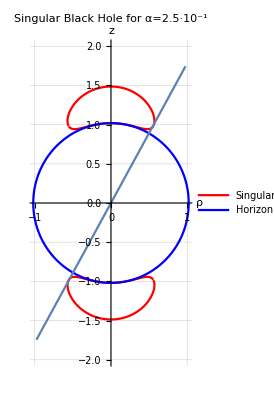

```mathematica
Legended[Show[{ParametricPlot[{(x+m)*Sqrt[1-y^2],(x+m)*y}/.Solve[(x^2 - y^2 + α^2 *(x- 1)^2)^2 - 4 * α^2 *y^2 *(x^2 - 1)==0,x][[3]],{y,-1,1},PlotStyle->Red,PlotLabel->"Singularity"],ParametricPlot[{-(x+m)*Sqrt[1-y^2],(x+m)*y}/.Solve[(x^2 - y^2 + α^2 *(x- 1)^2)^2 - 4 * α^2 *y^2 *(x^2 - 1)==0,x][[3]],{y,-1,1},PlotStyle->Red],ParametricPlot[{(x+m)*Sqrt[1-y^2],(x+m)*y}/.Solve[(x^2 - y^2 + α^2 *(x- 1)^2)^2 - 4 * α^2 *y^2 *(x^2 - 1)==0,x][[4]],{y,-1,1},PlotStyle->Red],ParametricPlot[{-(x+m)*Sqrt[1-y^2],(x+m)*y}/.Solve[(x^2 - y^2 + α^2 *(x- 1)^2)^2 - 4 * α^2 *y^2 *(x^2 - 1)==0,x][[4]],{y,-1,1},PlotStyle->Red]},{ParametricPlot[{(x+m)*Sqrt[1-y^2],(x+m)*y}/.x->1,{y,-1,1},PlotStyle->Blue],ParametricPlot[{-(x+m)*Sqrt[1-y^2],(x+m)*y}/.x->1,{y,-1,1},PlotStyle->Blue,PlotLabel->"Horizon"]},ParametricPlot[{t*Sqrt[1-0.8724636752516588^2],t*0.8724636752516588},{t,-2,2}],PlotRange->{-2,2},AxesOrigin->{0,0},PlotLabel->Style["Singular Black Hole for α=2.5·10^-1",Black],AxesLabel->{Style["ρ",Black,Bold],Style["z",Black,Bold]},GridLines->{Range[-2.1,2.1,0.1],Range[-|2.2,2.2,0.1]},Frame->False],LineLegend[{Red,Blue},{"Singularity","Horizon"}]]
```

```mathematica
Solve[(x^2 - y^2 + α^2 *(x- 1)^2)^2 - 4 * α^2 *y^2 *(x^2 - 1)==0/.{y->1,α->0.1},x]
```

{{x→-0.990098-0.017036 ⅈ},{x→-0.990098+0.017036 ⅈ},{x→1.},{x→1.0198}}

```mathematica
Xtil[x_] = x + 2*Log[x-1]
```

x+2 Log[-1+x]

```mathematica
Xtil[x/.Solve[(x^2 - y^2 + α^2 *(x- 1)^2)^2 - 4 * α^2 *y^2 *(x^2 - 1)==0/.{y->1,α->0.012},x]]
```

{0.386296-6.28318 ⅈ,0.386296+6.28318 ⅈ,-65.6056+6.28319 ⅈ,-10.0181}

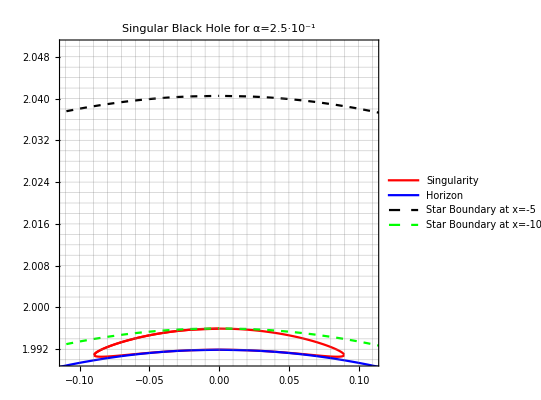

```mathematica
Legended[Show[{ParametricPlot[{(x+m)*Sqrt[1-y^2],(x+m)*y}/.Solve[(x^2 - y^2 + α^2 *(x- 1)^2)^2 - 4 * α^2 *y^2 *(x^2 - 1)==0,x][[3]],{y,0.995,1},PlotStyle->Red,PlotLabel->"Singularity",PlotPoints->200,MaxRecursion->2],ParametricPlot[{-(x+m)*Sqrt[1-y^2],(x+m)*y}/.Solve[(x^2 - y^2 + α^2 *(x- 1)^2)^2 - 4 * α^2 *y^2 *(x^2 - 1)==0,x][[3]],{y,0.995,1},PlotStyle->Red,PlotPoints->200,MaxRecursion->2],ParametricPlot[{(x+m)*Sqrt[1-y^2],(x+m)*y}/.Solve[(x^2 - y^2 + α^2 *(x- 1)^2)^2 - 4 * α^2 *y^2 *(x^2 - 1)==0,x][[4]],{y,0.995,1},PlotStyle->Red,PlotPoints->200,MaxRecursion->2],ParametricPlot[{-(x+m)*Sqrt[1-y^2],(x+m)*y}/.Solve[(x^2 - y^2 + α^2 *(x- 1)^2)^2 - 4 * α^2 *y^2 *(x^2 - 1)==0,x][[4]],{y,0.995,1},PlotStyle->Red,PlotPoints->200]},{ParametricPlot[{(x+m)*Sqrt[1-y^2],(x+m)*y}/.x->1,{y,0.99,1},PlotStyle->Blue,PlotPoints->50,PlotPoints->50,MaxRecursion->2],ParametricPlot[{-(x+m)*Sqrt[1-y^2],(x+m)*y}/.x->1,{y,0.99,1},PlotStyle->Blue,PlotLabel->"Horizon",PlotPoints->50,MaxRecursion->2]},ParametricPlot[{-(x+m)*Sqrt[1-y^2],(x+m)*y}/.Solve[(x^2 - y^2 + α^2 *(x- 1)^2)^2 - 4 * α^2 *y^2 *(x^2 - 1)==0,x][[4]],{y,0.99,1},PlotStyle->Red,PlotPoints->50,MaxRecursion->2],{ParametricPlot[{(x+m)*Sqrt[1-y^2],(x+m)*y}/.x->InverseXtilde[-10],{y,0.99,1},PlotStyle->{Green,Dashed},PlotPoints->50,MaxRecursion->2],ParametricPlot[{-(x+m)*Sqrt[1-y^2],(x+m)*y}/.x->InverseXtilde[-10],{y,0.99,1},PlotStyle->{Green,Dashed},PlotPoints->50,MaxRecursion->2,PlotLabel->"Horizon"]},{ParametricPlot[{(x+m)*Sqrt[1-y^2],(x+m)*y}/.x->InverseXtilde[-5],{y,0.99,1},PlotStyle->{Black,Dashed},PlotPoints->50,MaxRecursion->2],ParametricPlot[{-(x+m)*Sqrt[1-y^2],(x+m)*y}/.x->InverseXtilde[-5],{y,0.99,1},PlotStyle->{Black,Dashed},PlotPoints->50,MaxRecursion->2,PlotLabel->"Horizon"]},PlotRange->{{-0.11,0.11},{1.99,2.05}},AxesOrigin->{0,0},PlotLabel->Style["Singular Black Hole for α=2.5·10^-1",Black],GridLines->{Range[-0.11,0.11,0.01],Range[1.988,2.052,0.002]},ImageSize->{400,400},AspectRatio->Full,Frame->True],LineLegend[{Red,Blue,{Black, Dashed},{Green, Dashed}},{"Singularity","Horizon","Star Boundary at x=-5","Star Boundary at x=-10"}]]
```

```mathematica
InverseXtilde[x_]=2*LambertW[Sqrt[E^ (x-1)]/2]+1
```

1+2 ProductLog[1/2 √(ⅇ^(-1+x))]

```mathematica
InverseXtilde[-5]
```

1+2 ProductLog[1/(2 ⅇ^3)]

```mathematica
α=0.1
```

0.1

```mathematica
k=1
```

1

```mathematica
Plot[ρ[x,0.9999999],{x,1.02,1.6}]
```

$Aborted

```mathematica
ρ[1.02,0.9999999]
```

-2.69783×10^28

```mathematica
NSolve[{ρ[x,0.9999999]==0,x>=0},{x}]
```

$Aborted

```mathematica
FindRoot[ρ[x,0.9999999],{x,1.4,1,1.5}]
```

FindRoot::reged: The point {1.5} is at the edge of the search region {1.,1.5} in coordinate 1 and the computed search direction points outside the region.

{x→1.5}